```mathematica
ClearAll["Global`*"]
```

## Beginning stuff

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Initialize J-V, J_E-V data

```mathematica
orbit=1612;
```

```mathematica
makePlots=1;
```

#### pot offset (in V)?

```mathematica
potTFactor=0;
```

```mathematica
If[potTFactor == 0,potFactorString="",potFactorString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

#### Spectra average interval?

```mathematica
spectraAverageInterval=2;
```

```mathematica
specAvgItvlString=If[spectraAverageInterval==2,"",ToString@StringForm["-avgItvl`1`",spectraAverageInterval]];
```

### And the data ...

```mathematica
peakEBoundsIndShift=0;
```

```mathematica
peakEBoundsIndShift=False;
```

#### peakEBounds shift selection and string setup

```mathematica
peakEBoundsSuff="";If[ToString[Head[peakEBoundsIndShift]]=="Integer",peakEBoundsSuff=ToString@StringForm["-peakE_indShift_eq_`1`",peakEBoundsIndShift]];
```

#### These are derived using peakE_bounds_indShift=[-2,0]

```mathematica
If[peakEBoundsIndShift==-2,
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.600,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.490,0.475,0.672,0.578,0.552,0.490,0.472,0.426,0.430,0.274,0.304,0.090,0.055,0.125,0.135,0.268,0.285,0.410,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.370,0.467,0.610,0.658,0.637,0.519,0.850,1.349,1.119,1.174,1.449,1.167,1.240,1.101,1.041,0.754,0.546,0.732,0.820,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.940,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.700,0.846,0.849,0.941,0.911};
curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.040,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.040,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.110,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.060,0.081,0.057,0.049,0.050,0.040,0.027,0.040,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};
jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.720,0.704,0.693,0.630,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.590,0.636,0.510,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.370,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.190,0.136,0.200,0.198,0.210,0.256,0.193,0.276,0.269,0.200,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.590,0.540,0.453,0.450,0.318,0.261,0.300,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.880,0.796,0.675,0.753,0.648,0.572,0.608,0.560,0.378,0.305,0.374,0.188,0.188,0.214,0.310,0.280,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};
jeErrs={0.189,0.262,0.220,0.210,0.242,1.602,0.174,0.151,0.190,0.152,0.131,0.087,0.110,0.112,0.105,0.090,0.114,0.095,0.106,0.096,0.101,0.117,0.190,0.230,0.240,0.310,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.080,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.060,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.140,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.070,0.062,0.066,0.085,0.129,0.133,0.190,0.139,0.177,0.177,0.180,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.090,0.080,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.290,0.308,0.166,0.188,0.190,0.109,0.128,0.130,0.088,0.116,0.109,0.060,0.090,0.090,0.095,0.130,0.196,0.315,0.132};

gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};

kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
4,
time=Null;]]
```

If[False==-2,Switch[spectraAverageInterval,
2,time={12:00:24.114,12:00:24.745,12:00:25.376,12:00:26.006,12:00:26.637,12:00:27.268,12:00:27.898,12:00:28.529,12:00:29.159,12:00:29.790,12:00:30.421,12:00:31.051,12:00:31.682,12:00:32.313,12:00:32.943,12:00:33.574,12:00:34.205,12:00:34.835,12:00:35.466,12:00:36.096,12:00:36.727,12:00:37.358,12:00:37.988,12:00:38.619,12:00:39.250,12:00:39.880,12:00:40.511,12:00:41.142,12:00:41.772,12:00:42.403,12:00:43.033,12:00:43.664,12:00:44.295,12:00:44.925,12:00:45.556,12:00:46.187,12:00:46.817,12:00:47.448,12:00:48.079,12:00:48.709,12:00:49.340,12:00:49.971,12:00:50.601,12:00:51.232,12:00:51.863,12:00:52.493,12:00:53.124,12:00:53.755,12:00:54.385,12:00:55.016,12:00:55.647,12:00:56.277,12:00:56.908,12:00:57.539,12:00:58.169,12:00:58.800,12:00:59.431,12:01:00.061,12:01:00.692,12:01:01.323,12:01:01.953,12:01:02.584,12:01:03.215,12:01:03.845,12:01:04.476,12:01:05.107,12:01:05.737,12:01:06.368,12:01:06.999,12:01:07.629,12:01:08.260,12:01:08.891,12:01:09.521,12:01:10.152,12:01:10.783,12:01:11.413,12:01:12.044,12:01:12.675,12:01:13.305,12:01:13.936,12:01:14.567,12:01:15.197,12:01:15.828,12:01:16.459,12:01:17.090,12:01:17.720,12:01:18.351,12:01:18.982,12:01:19.612,12:01:20.243,12:01:20.874,12:01:21.504,12:01:22.135,12:01:22.766,12:01:23.397,12:01:24.027,12:01:24.658,12:01:25.289,12:01:25.919,12:01:26.550,12:01:27.181,12:01:27.811,12:01:28.442,12:01:29.073,12:01:29.703,12:01:30.334,12:01:30.965,12:01:31.596,12:01:32.226,12:01:32.857,12:01:33.488,12:01:34.118,12:01:34.749,12:01:35.380,12:01:36.010,12:01:36.641,12:01:37.272,12:01:37.903,12:01:38.533,12:01:39.164,12:01:39.795,12:01:40.425,12:01:41.056,12:01:41.687,12:01:42.318,12:01:42.948,12:01:43.579,12:01:44.210,12:01:44.840,12:01:45.471,12:01:46.102,12:01:46.733};pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.,777.28,777.28,840.,913.92,913.92,1012.48,1086.4,951.58,940.8,689.92,960.96,934.08,1133.44,1008.,1008.,1133.44,1133.44,1133.44,1008.,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.2,407.68,407.68,344.96,203.84,235.2,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.2,235.2,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.8,913.92,913.92,913.92,913.92,913.92,616.,616.,566.72,529.76,393.12,346.08,282.24,235.2,235.2,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.8,655.2,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.7,197.68,302.96,337.68,362.32,309.96,293.02};curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.6,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.49,0.475,0.672,0.578,0.552,0.49,0.472,0.426,0.43,0.274,0.304,0.09,0.055,0.125,0.135,0.268,0.285,0.41,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.37,0.467,0.61,0.658,0.637,0.519,0.85,1.349,1.119,1.174,1.449,1.167,1.24,1.101,1.041,0.754,0.546,0.732,0.82,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.94,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.7,0.846,0.849,0.941,0.911};curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.04,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.04,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.11,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.06,0.081,0.057,0.049,0.05,0.04,0.027,0.04,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.72,0.704,0.693,0.63,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.59,0.636,0.51,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.37,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.19,0.136,0.2,0.198,0.21,0.256,0.193,0.276,0.269,0.2,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.59,0.54,0.453,0.45,0.318,0.261,0.3,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.88,0.796,0.675,0.753,0.648,0.572,0.608,0.56,0.378,0.305,0.374,0.188,0.188,0.214,0.31,0.28,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};jeErrs={0.189,0.262,0.22,0.21,0.242,1.602,0.174,0.151,0.19,0.152,0.131,0.087,0.11,0.112,0.105,0.09,0.114,0.095,0.106,0.096,0.101,0.117,0.19,0.23,0.24,0.31,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.08,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.06,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.14,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.07,0.062,0.066,0.085,0.129,0.133,0.19,0.139,0.177,0.177,0.18,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.09,0.08,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.29,0.308,0.166,0.188,0.19,0.109,0.128,0.13,0.088,0.116,0.109,0.06,0.09,0.09,0.095,0.13,0.196,0.315,0.132};gaussbulkEs={1025.15,172.48,885.6,971.46,107.32,956.19,905.23,470.4,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.5,370.94,235.2,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.2,262.3,235.2,235.2,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.2,152.06,137.11,203.84,235.2,301.81,363.67,453.22,413.81,501.17,517.04,519.5,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.2,233.5,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.4,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.2,203.84,191.86};kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.9,576.64,586.45,589.13,584.9,512.07,397.18,370.06,309.72,299.35,235.2,203.84,123.5,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.1,119.64,148.07,140.6,266.94,134.04,195.7,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.8,400.8,398.67,388.12,281.6,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.5,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.8,348.09,316.43,336.57,219.13,141.12,91.9,202.7,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.4,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
4,time=Null;]]

#### These are derived using peakE_bounds_indShift=[0,0]

```mathematica
If[peakEBoundsIndShift==0,
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.600,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.490,0.475,0.672,0.578,0.552,0.490,0.472,0.426,0.430,0.274,0.304,0.090,0.055,0.125,0.135,0.268,0.285,0.410,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.370,0.467,0.610,0.658,0.637,0.519,0.850,1.349,1.119,1.174,1.449,1.167,1.240,1.101,1.041,0.754,0.546,0.732,0.820,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.940,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.700,0.846,0.849,0.941,0.911};
curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.040,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.040,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.110,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.060,0.081,0.057,0.049,0.050,0.040,0.027,0.040,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};
jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.720,0.704,0.693,0.630,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.590,0.636,0.510,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.370,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.190,0.136,0.200,0.198,0.210,0.256,0.193,0.276,0.269,0.200,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.590,0.540,0.453,0.450,0.318,0.261,0.300,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.880,0.796,0.675,0.753,0.648,0.572,0.608,0.560,0.378,0.305,0.374,0.188,0.188,0.214,0.310,0.280,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};
jeErrs={0.189,0.262,0.220,0.210,0.242,1.602,0.174,0.151,0.190,0.152,0.131,0.087,0.110,0.112,0.105,0.090,0.114,0.095,0.106,0.096,0.101,0.117,0.190,0.230,0.240,0.310,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.080,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.060,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.140,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.070,0.062,0.066,0.085,0.129,0.133,0.190,0.139,0.177,0.177,0.180,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.090,0.080,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.290,0.308,0.166,0.188,0.190,0.109,0.128,0.130,0.088,0.116,0.109,0.060,0.090,0.090,0.095,0.130,0.196,0.315,0.132};
gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};
kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
4,
time=Null;]]
```

If[False==0,Switch[spectraAverageInterval,
2,time={12:00:24.114,12:00:24.745,12:00:25.376,12:00:26.006,12:00:26.637,12:00:27.268,12:00:27.898,12:00:28.529,12:00:29.159,12:00:29.790,12:00:30.421,12:00:31.051,12:00:31.682,12:00:32.313,12:00:32.943,12:00:33.574,12:00:34.205,12:00:34.835,12:00:35.466,12:00:36.096,12:00:36.727,12:00:37.358,12:00:37.988,12:00:38.619,12:00:39.250,12:00:39.880,12:00:40.511,12:00:41.142,12:00:41.772,12:00:42.403,12:00:43.033,12:00:43.664,12:00:44.295,12:00:44.925,12:00:45.556,12:00:46.187,12:00:46.817,12:00:47.448,12:00:48.079,12:00:48.709,12:00:49.340,12:00:49.971,12:00:50.601,12:00:51.232,12:00:51.863,12:00:52.493,12:00:53.124,12:00:53.755,12:00:54.385,12:00:55.016,12:00:55.647,12:00:56.277,12:00:56.908,12:00:57.539,12:00:58.169,12:00:58.800,12:00:59.431,12:01:00.061,12:01:00.692,12:01:01.323,12:01:01.953,12:01:02.584,12:01:03.215,12:01:03.845,12:01:04.476,12:01:05.107,12:01:05.737,12:01:06.368,12:01:06.999,12:01:07.629,12:01:08.260,12:01:08.891,12:01:09.521,12:01:10.152,12:01:10.783,12:01:11.413,12:01:12.044,12:01:12.675,12:01:13.305,12:01:13.936,12:01:14.567,12:01:15.197,12:01:15.828,12:01:16.459,12:01:17.090,12:01:17.720,12:01:18.351,12:01:18.982,12:01:19.612,12:01:20.243,12:01:20.874,12:01:21.504,12:01:22.135,12:01:22.766,12:01:23.397,12:01:24.027,12:01:24.658,12:01:25.289,12:01:25.919,12:01:26.550,12:01:27.181,12:01:27.811,12:01:28.442,12:01:29.073,12:01:29.703,12:01:30.334,12:01:30.965,12:01:31.596,12:01:32.226,12:01:32.857,12:01:33.488,12:01:34.118,12:01:34.749,12:01:35.380,12:01:36.010,12:01:36.641,12:01:37.272,12:01:37.903,12:01:38.533,12:01:39.164,12:01:39.795,12:01:40.425,12:01:41.056,12:01:41.687,12:01:42.318,12:01:42.948,12:01:43.579,12:01:44.210,12:01:44.840,12:01:45.471,12:01:46.102,12:01:46.733};pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.,777.28,777.28,840.,913.92,913.92,1012.48,1086.4,951.58,940.8,689.92,960.96,934.08,1133.44,1008.,1008.,1133.44,1133.44,1133.44,1008.,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.2,407.68,407.68,344.96,203.84,235.2,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.2,235.2,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.8,913.92,913.92,913.92,913.92,913.92,616.,616.,566.72,529.76,393.12,346.08,282.24,235.2,235.2,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.8,655.2,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.7,197.68,302.96,337.68,362.32,309.96,293.02};curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.6,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.49,0.475,0.672,0.578,0.552,0.49,0.472,0.426,0.43,0.274,0.304,0.09,0.055,0.125,0.135,0.268,0.285,0.41,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.37,0.467,0.61,0.658,0.637,0.519,0.85,1.349,1.119,1.174,1.449,1.167,1.24,1.101,1.041,0.754,0.546,0.732,0.82,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.94,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.7,0.846,0.849,0.941,0.911};curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.04,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.04,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.11,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.06,0.081,0.057,0.049,0.05,0.04,0.027,0.04,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.72,0.704,0.693,0.63,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.59,0.636,0.51,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.37,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.19,0.136,0.2,0.198,0.21,0.256,0.193,0.276,0.269,0.2,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.59,0.54,0.453,0.45,0.318,0.261,0.3,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.88,0.796,0.675,0.753,0.648,0.572,0.608,0.56,0.378,0.305,0.374,0.188,0.188,0.214,0.31,0.28,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};jeErrs={0.189,0.262,0.22,0.21,0.242,1.602,0.174,0.151,0.19,0.152,0.131,0.087,0.11,0.112,0.105,0.09,0.114,0.095,0.106,0.096,0.101,0.117,0.19,0.23,0.24,0.31,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.08,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.06,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.14,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.07,0.062,0.066,0.085,0.129,0.133,0.19,0.139,0.177,0.177,0.18,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.09,0.08,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.29,0.308,0.166,0.188,0.19,0.109,0.128,0.13,0.088,0.116,0.109,0.06,0.09,0.09,0.095,0.13,0.196,0.315,0.132};gaussbulkEs={1025.15,172.48,885.6,971.46,107.32,956.19,905.23,470.4,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.5,370.94,235.2,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.2,262.3,235.2,235.2,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.2,152.06,137.11,203.84,235.2,301.81,363.67,453.22,413.81,501.17,517.04,519.5,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.2,233.5,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.4,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.2,203.84,191.86};kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.9,576.64,586.45,589.13,584.9,512.07,397.18,370.06,309.72,299.35,235.2,203.84,123.5,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.1,119.64,148.07,140.6,266.94,134.04,195.7,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.8,400.8,398.67,388.12,281.6,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.5,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.8,348.09,316.43,336.57,219.13,141.12,91.9,202.7,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.4,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
4,time=Null;]]

#### These are derived using NO peakE_bounds _indShift

```mathematica
If[(ToString@Head[peakEBoundsIndShift])≠ "Integer",
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={1.367,1.545,1.618,1.661,1.901,1.554,1.211,0.916,0.980,1.144,1.071,0.973,0.965,0.930,0.922,0.911,0.791,0.803,0.839,0.821,0.864,0.892,1.413,2.020,1.934,1.000,0.984,0.809,0.788,0.835,0.867,0.862,0.859,0.788,0.810,0.774,0.712,0.611,0.554,0.531,0.570,0.451,0.344,0.160,0.137,0.147,0.181,0.330,0.396,0.506,0.506,0.542,0.508,0.524,0.540,0.613,0.395,0.602,0.594,0.601,0.830,0.630,0.838,0.802,0.502,0.289,0.480,0.797,0.946,1.128,0.782,0.787,1.310,1.663,1.875,1.979,1.908,1.867,1.720,1.476,1.580,0.973,0.599,0.803,1.067,1.181,1.666,1.870,2.026,1.509,1.794,1.793,1.771,1.618,1.696,1.473,1.342,1.384,1.317,1.177,1.250,1.166,0.984,0.783,0.834,0.317,0.283,0.357,0.574,0.496,0.707,1.759,2.297,2.559,2.346,1.343,1.262,1.297,1.241,1.245,1.263,0.804,1.221,0.949,0.745,0.533,0.383,1.008,1.076,1.034,1.245,1.342};
curErrs={0.054,0.061,0.056,0.058,0.059,0.053,0.044,0.042,0.041,0.057,0.046,0.035,0.035,0.041,0.047,0.041,0.049,0.040,0.039,0.039,0.043,0.041,0.061,0.077,0.088,0.065,0.050,0.044,0.042,0.056,0.054,0.054,0.052,0.055,0.056,0.047,0.048,0.043,0.045,0.050,0.055,0.059,0.038,0.038,0.022,0.039,0.032,0.041,0.045,0.075,0.048,0.047,0.048,0.062,0.057,0.061,0.054,0.107,0.082,0.062,0.061,0.105,0.084,0.090,0.050,0.100,0.074,0.085,0.121,0.146,0.098,0.128,0.110,0.137,0.115,0.111,0.110,0.136,0.156,0.105,0.055,0.049,0.034,0.042,0.040,0.053,0.059,0.056,0.068,0.062,0.063,0.059,0.059,0.057,0.062,0.054,0.124,0.204,0.110,0.105,0.100,0.112,0.152,0.087,0.044,0.041,0.033,0.031,0.030,0.031,0.037,0.067,0.105,0.111,0.098,0.063,0.059,0.063,0.036,0.032,0.046,0.025,0.030,0.029,0.025,0.024,0.037,0.036,0.038,0.040,0.031,0.053};
jes={1.263,1.626,1.854,1.924,2.120,1.769,1.242,0.782,0.791,0.843,0.696,0.564,0.525,0.477,0.471,0.474,0.389,0.416,0.453,0.455,0.486,0.500,1.087,1.787,1.719,0.750,0.737,0.549,0.535,0.538,0.570,0.599,0.597,0.565,0.542,0.502,0.424,0.328,0.285,0.252,0.265,0.203,0.151,0.089,0.088,0.086,0.093,0.137,0.154,0.193,0.195,0.199,0.195,0.187,0.199,0.214,0.148,0.223,0.219,0.233,0.294,0.212,0.304,0.318,0.231,0.137,0.214,0.385,0.467,0.478,0.300,0.286,0.581,0.749,0.854,0.900,0.825,0.755,0.634,0.518,0.543,0.346,0.267,0.308,0.385,0.433,0.737,0.950,1.181,0.910,1.086,1.250,1.239,1.067,1.021,0.914,0.805,0.853,0.785,0.616,0.654,0.611,0.470,0.359,0.405,0.207,0.199,0.227,0.318,0.280,0.400,1.018,1.649,2.043,1.828,0.857,0.787,0.850,0.694,0.710,0.802,0.513,0.675,0.462,0.403,0.338,0.306,0.563,0.660,0.612,0.675,0.642};
jeErrs={0.101,0.121,0.123,0.124,0.120,0.137,0.118,0.162,0.170,0.159,0.123,0.078,0.076,0.077,0.106,0.075,0.110,0.078,0.084,0.077,0.090,0.084,0.129,0.147,0.163,0.166,0.112,0.094,0.091,0.131,0.138,0.143,0.122,0.124,0.123,0.096,0.087,0.095,0.080,0.071,0.079,0.107,0.044,0.056,0.042,0.323,0.049,0.048,0.082,0.076,0.098,0.060,0.124,0.144,0.455,0.073,0.054,0.188,0.113,1.244,0.094,0.117,0.091,0.189,0.075,0.208,0.273,0.121,0.195,0.233,0.112,0.142,0.244,0.230,0.162,0.166,0.170,0.168,0.313,0.115,0.078,0.058,0.067,0.059,0.061,0.074,0.110,0.106,0.158,0.128,0.149,0.151,0.145,0.155,0.146,0.128,0.264,0.529,0.220,0.185,0.205,0.195,0.357,0.105,0.065,0.068,0.074,0.055,0.060,0.116,0.138,0.115,0.216,0.245,0.204,0.132,0.144,0.156,0.092,0.121,0.112,0.086,0.090,0.093,0.061,0.090,0.090,0.088,0.113,0.150,0.154,0.112};
gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};
kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};
,
4,
time={"12:00:24.114","12:00:25.376","12:00:26.637","12:00:27.898","12:00:29.159","12:00:30.421","12:00:31.682","12:00:32.943","12:00:34.205","12:00:35.466","12:00:36.727","12:00:37.988","12:00:39.250","12:00:40.511","12:00:41.772","12:00:43.033","12:00:44.295","12:00:45.556","12:00:46.817","12:00:48.079","12:00:49.340","12:00:50.601","12:00:51.863","12:00:53.124","12:00:54.385","12:00:55.647","12:00:56.908","12:00:58.169","12:00:59.431","12:01:00.692","12:01:01.953","12:01:03.215","12:01:04.476","12:01:05.737","12:01:06.999","12:01:08.260","12:01:09.521","12:01:10.783","12:01:12.044","12:01:13.305","12:01:14.567","12:01:15.828","12:01:17.090","12:01:18.351","12:01:19.612","12:01:20.874","12:01:22.135","12:01:23.397","12:01:24.658","12:01:25.919","12:01:27.181","12:01:28.442","12:01:29.703","12:01:30.965","12:01:32.226","12:01:33.488","12:01:34.749","12:01:36.010","12:01:37.272","12:01:38.533","12:01:39.795","12:01:41.056","12:01:42.318","12:01:43.579","12:01:44.840","12:01:46.102"};
pots={940.80,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.00,777.28,913.92,913.92,1211.84,940.80,1059.52,1008.00,1008.00,1133.44,1008.00,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.20,282.24,407.68,407.68,235.20,368.06,447.72,358.82,282.24,235.20,141.12,203.84,407.68,562.80,700.00,835.52,913.92,913.92,913.92,616.00,417.76,346.08,235.20,189.42,581.42,832.30,717.64,655.20,364.98,358.82,249.06,161.14,315.28,393.12,309.96};
curs={1.497,1.609,1.714,1.095,1.076,1.017,0.945,0.931,0.817,0.818,0.868,1.660,1.580,0.902,0.804,0.866,0.852,0.784,0.664,0.549,0.532,0.264,0.140,0.246,0.462,0.511,0.509,0.562,0.496,0.596,0.746,0.820,0.438,0.617,0.989,0.790,1.507,1.891,1.879,1.619,1.346,0.682,1.111,1.760,1.868,1.760,1.688,1.614,1.399,1.237,1.199,0.901,0.633,0.311,0.535,1.146,2.466,1.914,1.260,1.244,1.101,1.088,0.639,0.661,1.087,1.261};
curErrs={0.045,0.046,0.042,0.033,0.037,0.035,0.027,0.035,0.035,0.032,0.031,0.052,0.062,0.041,0.034,0.040,0.042,0.045,0.033,0.034,0.044,0.029,0.020,0.026,0.044,0.042,0.037,0.042,0.058,0.066,0.049,0.065,0.044,0.083,0.084,0.080,0.094,0.103,0.081,0.097,0.042,0.031,0.032,0.044,0.052,0.051,0.043,0.045,0.114,0.102,0.073,0.090,0.032,0.027,0.023,0.038,0.087,0.071,0.044,0.026,0.030,0.023,0.019,0.024,0.030,0.030};
jes={1.475,1.855,1.914,1.056,0.829,0.635,0.504,0.484,0.411,0.447,0.489,1.372,1.342,0.654,0.536,0.583,0.599,0.518,0.381,0.273,0.244,0.123,0.086,0.113,0.177,0.193,0.190,0.204,0.186,0.225,0.260,0.310,0.202,0.287,0.455,0.297,0.676,0.861,0.791,0.587,0.470,0.283,0.405,0.835,1.104,1.129,1.152,0.984,0.849,0.704,0.627,0.425,0.331,0.208,0.298,0.666,1.860,1.415,0.800,0.704,0.697,0.583,0.368,0.421,0.655,0.663};
jeErrs={0.087,0.103,0.090,0.093,0.127,0.085,0.056,0.075,0.073,0.066,0.064,0.105,0.121,0.090,0.077,0.103,0.097,0.091,0.060,0.056,0.056,0.036,0.031,0.035,0.063,0.076,0.083,0.108,0.062,0.395,0.062,0.076,0.062,0.447,0.116,0.092,0.153,0.146,0.116,0.124,0.056,0.050,0.049,0.085,0.116,0.121,0.107,0.106,0.238,0.206,0.128,0.127,0.050,0.053,0.050,0.077,0.181,0.143,0.104,0.081,0.078,0.076,0.045,0.063,0.097,0.129};
]]
```

```mathematica
(*ListPlot[Partition[Riffle[jes,jeErrs],2]]*)
```

```mathematica
(*ListPlot[Partition[Riffle[jes,jeErrs],2]]*)
```

### And the interval …

```mathematica
Print[ToString@StringForm["spectraAvgItvl: `1`",spectraAverageInterval]];
Print[ToString@StringForm["peakEBoundsIndShift: `1`",peakEBoundsIndShift]];
```

spectraAvgItvl: 2

peakEBoundsIndShift: False

```mathematica
interval=2;
```

```mathematica
interval=1;
```

#### Upward ion beam times

```mathematica
Switch[spectraAverageInterval,
2,
upIonTidM1={"12:00:29.790","12:00:37.358"};,
4,
upIonTidM1={"12:00:29.2","12:00:36.727"};]
```

```mathematica
upIonTidM2={"12:00:46.000","12:00:49.000"};
```

```mathematica
upIonTidM4={"12:01:18.5","12:01:30"};
```

```mathematica
noBkgrndElec4={"12:01:20","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:24","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:17","12:01:23"};
```

```mathematica
Turnon={"12:01:11.4","12:01:22"};
```

```mathematica
ChrisRecommendedTimes={"12:01:20","12:01:30"};
```

```mathematica
{JimRecommendedTimes,JimRecommendedTimes2}={{"12:01:20","12:01:27"},{"12:01:10","12:01:15"}};
```

```mathematica
spenceTider={"12:01:24.568","12:01:29.073"};
```

```mathematica
spenceTider={"12:01:22.766","12:01:29.703"};
```

#### Finish setting up inds

```mathematica
itvl1Bounds={Flatten@((minTidInd[#,time])&/@upIonTidM1),Flatten@((minTidInd[#,time])&/@upIonTidM2)};
```

```mathematica
itvl1Inds=Flatten@MapThread[Range,Transpose@itvl1Bounds];
```

```mathematica
(*itvl2Users=noBkgrndClearLossCone;*)
```

```mathematica
(*itvl2Users=Turnon;*)
```

```mathematica
itvl2Users=ChrisRecommendedTimes;
```

```mathematica
itvl2Users=JimRecommendedTimes2;
```

```mathematica
itvl2Users=spenceTider;
```

```mathematica
itvl2Bounds=Flatten@((minTidInd[#,time])&/@itvl2Users);
```

```mathematica
itvl2Inds=Range@@itvl2Bounds;
```

Manip plots to decide on indices to use

#### Ze plots

```mathematica
pRange={{000,1400},{0,3}};
```

```mathematica
pRange={{000,Max[pots]*1.1},{0,Max[curs]*1.1}};
```

```mathematica
pRangeJe={{000,Max[pots]*1.1},{0,Max[jes]*1.2}};
```

```mathematica
manipInds=itvl2Inds;
ind1Start=1;ind1Init=manipInds[[1]];ind1EndInit=manipInds[[Round@(Length@manipInds/2)]];ind2Init=manipInds[[-1]];
```

```mathematica
{mType1,mType2,mType3}={1,2,"Manip"};
```

```mathematica
mType=1;
```

```mathematica
mType=2;
```

```mathematica
mType="Manip";
```

```mathematica
Switch[mType,
mType1,
Row[{tPlotInds[itvl1Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl1Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType2,
Row[{tPlotInds[itvl2Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl2Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType3,
Manipulate[Manipulate[
Row[{tPlotRange[ind1,ind2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotRange[ind1,ind2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]
```

### Make a movie

```mathematica
makeMovie=0;
saveMovie=0;
```

```mathematica
If[makeMovie==1,
{firstInd,lastInd1,lastInd2}={76,79,105};
plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];
plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];
If[saveMovie==1,
movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];
Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]];
tablePlotsCombineAndAnimate[plotMov,plotMov2]]
```

```mathematica
(*{firstInd,lastInd1,lastInd2}={76,79,105};*)
```

```mathematica
(*plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];*)
```

```mathematica
(*plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];*)
```

```mathematica
(*movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];*)
```

```mathematica
(*Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["orb1612__01_11_to_01_29.gif"]]]
```

AbsoluteFileName::fdnfnd: Directory or file orb1612__01_11_to_01_29.gif not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

```mathematica
ListAnimate[plotMov]
```

ListAnimate[plotMov]

## The fits—J-V, J_E-V, and combined

Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
(*True cavity #1, 2018/03/20 assays*)
```

```mathematica
inds1=Range[256,270]; 
inds2=Range[284,292];
```

#### Data set 1

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays*)
```

```mathematica
inds1=Range[232,249]+indShift;
inds2=Range[257,272]+indShift;
```

#### Data set 2

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[12,44]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[56,84];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[149,163];
```

```mathematica
inds2=Range[182,208];
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 3

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[74,81];
```

```mathematica
inds2=Range[91,104];
```

```mathematica
inds2=Range[88,122];
```

```mathematica
inds3={3,4}~Join~inds2;
```

```mathematica
inds1=Range[57,80];(*Buck wild!*)
```

```mathematica
inds1=Range[87,105]~Join~Range[115,121];(*Buck wild!*)
```

```mathematica
inds1=Range[76,89];
```

```mathematica
inds1=Range[78,81]~Join~Range[85,92];
```

#### Data set 4

```mathematica
doMaxwellian=1;
```

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
(*If[dataset==4,
If[doMaxwellian,
ind0Seg1=Range[6,22]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[28,42](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;(*END Maxwellian*),
],]*)
```

```mathematica
If[doMaxwellian==1,ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;
(*inds1=ind0Seg2;*)]
```

```mathematica
(*Now kappas*)
```

```mathematica
(*inds1=Range[33,44]~Join~Range[46,49];*)
```

```mathematica
inds1=Range[33,44];
```

```mathematica
(*inds2=Range[56,78]; *)
```

```mathematica
inds2=Range[57,70]; (*Just clean stuff, no scary-low potentials or anything*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 5

```mathematica
(*inds1=Range[46,53]~Join~Range[36,37];*)
```

### Instead, use intervals!

```mathematica
Switch[interval,1,inds1=itvl1Inds;inds2=itvl2Inds;,2,inds1=itvl2Inds;inds2=itvl1Inds;]
```

Fits: Initialize data, select indices to use, setup bounds and initial guesses

### Initialize plotData1, errorData1, plotDataWts1, etc. (takes stock of potTFactor)

Current data

```mathematica
{plotData1}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
{errorData1}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
{plotDataWts1}=(1/(curErrs[[#]])^2)&/@{inds1};
```

Energy flux data

```mathematica
{jeData1}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1};
```

```mathematica
{errorJe1}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1};
```

```mathematica
{jeDataWts1}=(1/(jeErrs[[#]])^2)&/@{inds1};
```

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

### Fix temperature?

```mathematica
doFixT=True;
Switch[interval,
1,
kFixT=140;
gFixT=120;,
2,
kFixT=180;
gFixT=140;
]
fixTSuff=If[doFixT==True,"-fixT",""];
```

### Bounds

```mathematica
minFitT=50;
maxFitT=1000;
minFitRB=2;
maxFitRB=1000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.51;
maxFitKappa=35.;
```

#### Set up constraints ...

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

### Initial guesses

```mathematica
kFitNinit=0.5;
kFitTinit=300;
kFitRBinit=If[10>maxFitRB,maxFitRB,10];
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=0.5;
gFitTinit=300;
gFitRBinit=If[10>maxFitRB,maxFitRB,10];
gFitRB1init=10;
gFitRB2init=10;
```

### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

Nonlinear J-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};,
kFitT=kFixT;
gFitT=gFixT;
kModel = JVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
kBestT=kFixT;
gBestT=gFixT;
{kBestN,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
]
```

Nonlinear J_E-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};,
kModelJeV = JEVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
{kBestJeVN,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
kBestJeVT=kFixT;
gBestJeVT=gFixT;]
```

Now J-V and J_E-V fits simultaneously!

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-4;
gCombDOF=Length[combDat[[;;,1]]]-3;
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFixT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFixT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-3;
gCombDOF=Length[combDat[[;;,1]]]-2;
kCombT=kFixT;
gCombT=gFixT;
{kCombRB,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};]
```

```mathematica
If[doFixT==False,gPlotStepMonitorData[gCombStepVals]](*gPlotStepMonitorData not meant to handle fixT situations*)
```

## Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=Max[pots[[indsInUse]]]*1.1;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=Max[curs[[indsInUse]]]*1.1;
```

```mathematica
minJe=0;maxJe=Max[jes[[indsInUse]]]*1.1;
```

### Setup combined fit plots

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestKappa,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJeVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestJeVKappa,3]])}~Join~kJeVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gCombVals~Join~{(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kCombVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],*)
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
doubledPref="twoIntervals__combJVJeVFit";
```

```mathematica
mkFN[fPref_,dir_]:=Module[{tmpFN,count},
count=1;
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,peakEBoundsSuff,specAvgItvlString];
While[FileExistsQ[dir<>tmpFN],
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9`__`10`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,specAvgItvlString,peakEBoundsSuff,NumberForm[count,1,NumberPadding->{"0", ""}]];
];
outFN=tmpFN]
```

```mathematica
{JVFilename,JeVFilename,combFilename,doubledFilename}=(mkFN[#,dir])&/@{JVPref,JeVPref,combPref,doubledPref}
```

{Orb1612__JVFit__inds_94-105__Automatic-fixT.png,Orb1612__JeVFit__inds_94-105__Automatic-fixT.png,Orb1612__combJVJeVFit__inds_94-105__Automatic-fixT.png,Orb1612__twoIntervals__combJVJeVFit__inds_94-105__Automatic-fixT.png}

### J-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,*)
```

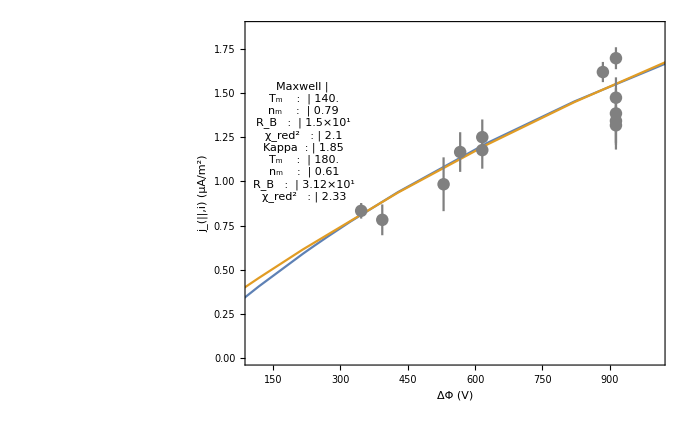

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),*)
```

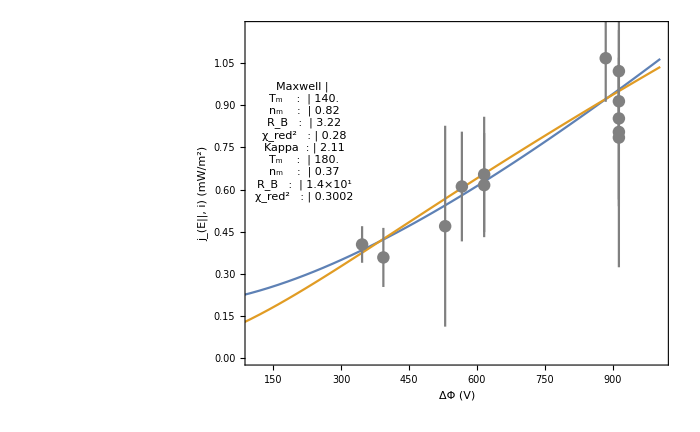

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

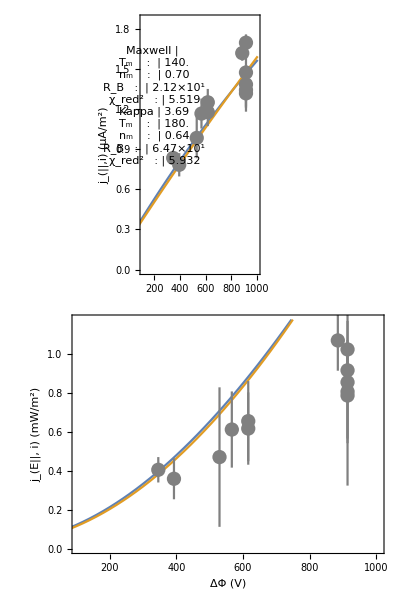

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

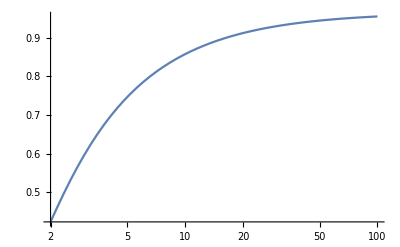

```mathematica
LogLinearPlot[LKMwellDensFac[100/50,RB],{RB,2,100},PlotRange->Full]
```

#### Save plots

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];
Print[JVFilename<>" ..."];
Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180330/ ...

Orb1612__JVFit__inds_94-105__Automatic-fixT.png ...

Orb1612__JeVFit__inds_94-105__Automatic-fixT.png ...

Orb1612__combJVJeVFit__inds_94-105__Automatic-fixT.png ...

Done!